# Tree-level graviton scattering with FeynArts

Generate and display all four off-shell 2 -> 2 graviton tree diagrams with FeynArts: the three exchange channels and the quartic contact. Attach unconstrained external polarisation tensors, contract each contribution, and store their sum in ℳ. No mass-shell, transversality, tracelessness or helicity conditions are imposed.

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the two cells below with Shift+Enter. The first loads FeynGrav, which loads FeynCalc and CalcFormConverter, and asks FeynCalc to load the installed patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. GenericModel is given explicitly because the classes file does not name its generic model and the FeynArts default is the stock "Lorentz" file. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

```mathematica
grModel="PureGR";
InitializeModel[grModel,GenericModel->grModel];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

```mathematica
grModel="PureGR";
InitializeModel[grModel,GenericModel->grModel];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the two cells below with Shift+Enter. The first loads FeynGrav, which loads FeynCalc and CalcFormConverter, and asks FeynCalc to load the installed patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. GenericModel is given explicitly because the classes file does not name its generic model and the FeynArts default is the stock "Lorentz" file. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

```mathematica
grModel="PureGR";
InitializeModel[grModel,GenericModel->grModel];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

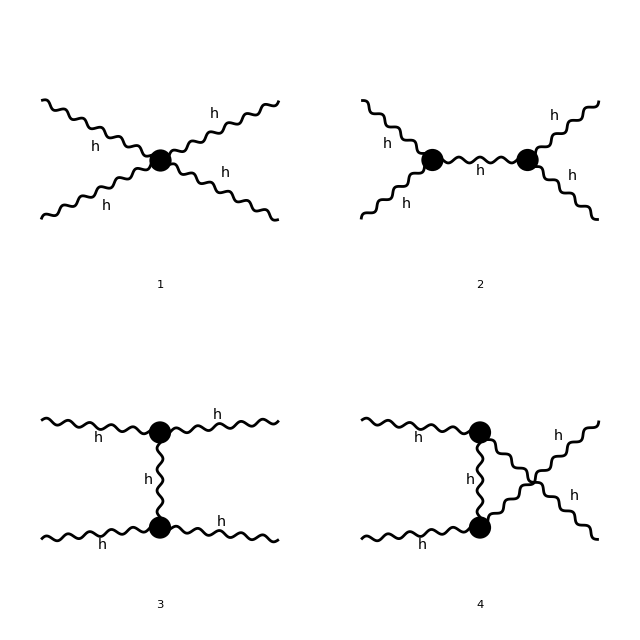

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 4. Contract each diagram and form the total ℳ

Contract the diagrams separately with FORM to limit intermediate expression sizes. The list diagramAmplitudes retains the individual scalar-product expressions. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced. Each contraction uses CalcFormCalculate with its default options: the Lorentz dimension is inferred from the expression, which carries symbolic D, and successful FORM jobs are cleaned up automatically. The results are checked for a surviving Lorentz index or an unconverted head before the total is formed.

```mathematica
theAmplitude[p1_,p2_,p3_,p4_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;
```

The complete polarisation-contracted, amputated off-shell tree expression is stored in ℳ (Mathematica's ScriptCapitalM symbol). Its preview below is shortened only for display. This is not yet an on-shell physical scattering amplitude: the external virtualities, longitudinal contractions and trace terms remain unconstrained. No loop measure or spin sum is included.

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·(«3»)^*(p4)) («2»«1»«1»)^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D «6» κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·(«3»)^*(p4)) («2»«1»«1»)^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D «6» κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

```mathematica
theAmplitude[p1,p2,p3,p4]==theAmplitude[p2,p1,p3,p4]//CalcFormCalculate
```

```mathematica
theAmplitude[p1,p2,p3,p4]==theAmplitude[p2,p1,p3,p4]//CalcFormCalculate
```

## 4. Contract each diagram and form the total ℳ

Contract the diagrams separately with FORM to limit intermediate expression sizes. The list diagramAmplitudes retains the individual scalar-product expressions. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced. Each contraction uses CalcFormCalculate with its default options: the Lorentz dimension is inferred from the expression, which carries symbolic D, and successful FORM jobs are cleaned up automatically. The results are checked for a surviving Lorentz index or an unconverted head before the total is formed.

```mathematica
theAmplitude[p1_,p2_,p3_,p4_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;
```

The complete polarisation-contracted, amputated off-shell tree expression is stored in ℳ (Mathematica's ScriptCapitalM symbol). Its preview below is shortened only for display. This is not yet an on-shell physical scattering amplitude: the external virtualities, longitudinal contractions and trace terms remain unconstrained. No loop measure or spin sum is included.

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·(«3»)^*(p4)) («2»«1»«1»)^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D «6» κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

```mathematica
theAmplitude[p1,p2,p3,p4]==theAmplitude[p2,p1,p3,p4]//CalcFormCalculate
```

# Tree-level graviton scattering with FeynArts

Generate and display all four off-shell 2 -> 2 graviton tree diagrams with FeynArts: the three exchange channels and the quartic contact. Attach unconstrained external polarisation tensors, contract each contribution, and store their sum in ℳ. No mass-shell, transversality, tracelessness or helicity conditions are imposed.

## 1. Initialisation

Start with a fresh kernel (especially after running the previous on-shell version) and evaluate the two cells below with Shift+Enter. The first loads FeynGrav, which loads FeynCalc and CalcFormConverter, and asks FeynCalc to load the installed patched FeynArts. The saved pure-GR model uses gauge parameter 2 and contains the cubic and quartic graviton interactions and gravitational ghosts. GenericModel is given explicitly because the classes file does not name its generic model and the FeynArts default is the stock "Lorentz" file. No diagrams are generated and FORM is not executed here. Opening this notebook executes nothing.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialisation, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

```mathematica
grModel="PureGR";
InitializeModel[grModel,GenericModel->grModel];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.gen

> $GenericMixing is OFF

generic model {PureGR} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/PureGR.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {PureGR} initialized

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->grModel,GenericModel->grModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1,p2 and outgoing momenta p3,p4. All virtualities and scalar products remain symbolic. MomentumConservation -> True supplies internal routing at each vertex without imposing mass-shell conditions or eliminating an external momentum. Truncated -> True removes external propagators; polarisations are attached explicitly in the next cell.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,GaugeRules->{},MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 4. Contract each diagram and form the total ℳ

Contract the diagrams separately with FORM to limit intermediate expression sizes. The list diagramAmplitudes retains the individual scalar-product expressions. No scalar-product assignments, helicity tables, mass-shell conditions or extra graph factors are introduced. Each contraction uses CalcFormCalculate with its default options: the Lorentz dimension is inferred from the expression, which carries symbolic D, and successful FORM jobs are cleaned up automatically. The results are checked for a surviving Lorentz index or an unconverted head before the total is formed.

```mathematica
theAmplitude[p1_,p2_,p3_,p4_]=(CalcFormCalculate[FeynAmpDenominatorExplicit[#1] externalTensors]&)/@diagramTensors//Total;
```

The complete polarisation-contracted, amputated off-shell tree expression is stored in ℳ (Mathematica's ScriptCapitalM symbol). Its preview below is shortened only for display. This is not yet an on-shell physical scattering amplitude: the external virtualities, longitudinal contractions and trace terms remain unconstrained. No loop measure or spin sum is included.

```mathematica
Short[theAmplitude[p1,p2,p3,p4],4]
```

(ⅈ D (p1·ε^*(p4)) (p2·ε^*(p4)) (p3·ε^*(p3))^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))-(2 ⅈ (p1·ε^*(p4)) (p2·(«3»)^*(p4)) («2»«1»«1»)^2 (ε(p1)·ε(p2))^2 κ^2)/((D-2) (p2^2-2 (p2·p3)+p3^2))+«23356»+(ⅈ D «6» κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))-(2 ⅈ (p1·ε(p2)) (p2·ε(p1)) (p3·ε(p1)) (p3·ε(p2)) (ε^*(p3))^2 (ε^*(p4))^2 κ^2)/((D-2) (p3^2+2 (p3·p4)+p4^2))

```mathematica
theAmplitude[p1,p2,p3,p4]//Length
```

15576

```mathematica
theAmplitude[p1,p2,p3,p4]==theAmplitude[p2,p1,p3,p4]//CalcFormCalculate
```